# Discrete Fourier transform

```mathematica
Needs["FourierSeries`"]
```

```mathematica
Clear["Global`*"]
```

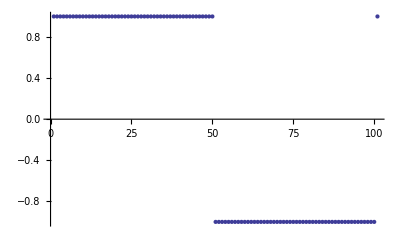

```mathematica
data=Table[SquareWave[{-1,1},x],{x,0,1,0.01}];
n=Length[data];
ListPlot[data]
```

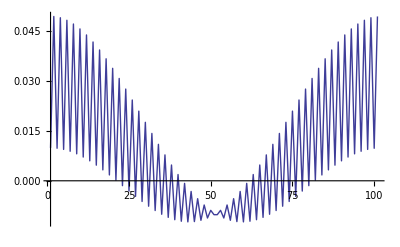

```mathematica
dct=Fourier[data,FourierParameters->{-1,1}];
ListLinePlot[Re[dct],PlotRange->All]
```

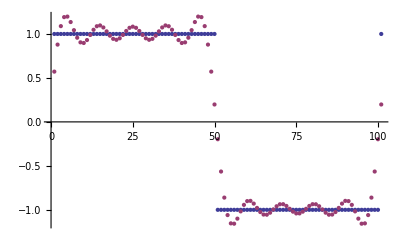

```mathematica
tdata=2Fourier[PadRight[Take[dct,10],n,0],FourierParameters->{1,-1}];
ListPlot[{data,Re[tdata]}]
```